```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\fluc_T\fluctuations_T\highorder_2p1\input_h\finitemub

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../LQCDdata/hotdpt4u.dat"]];
Tcl=1;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

```mathematica
mub={0,100,200,300,400};
T=Table[i,{i,21,300}];
poT4data=Table[(Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi0.dat"]]-Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi0.dat"]][[1]])/T^4,{i,1,Length[mub]}];
c2data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c2.dat"]],{i,1,Length[mub]}];
c3data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c3.dat"]],{i,1,Length[mub]}];
c4data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c4.dat"]],{i,1,Length[mub]}];
c5data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c5.dat"]],{i,1,Length[mub]}];
c6data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c6.dat"]],{i,1,Length[mub]}];
```

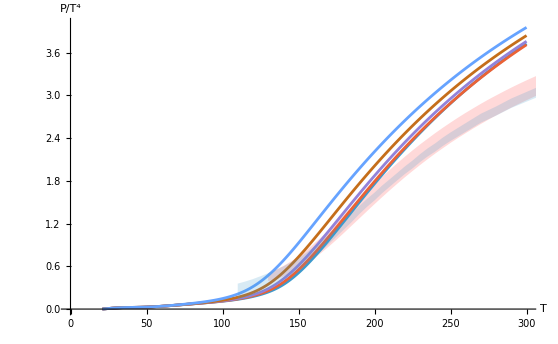

```mathematica
PlotP=Show[ListLinePlot[{Transpose[{T,poT4data[[1]]}],Hotpdown,Hotpup,Transpose[{T,poT4data[[2]]}],Transpose[{T,poT4data[[3]]}],Transpose[{T,poT4data[[4]]}],Transpose[{T,poT4data[[5]]}]},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None,Automatic,Automatic,Automatic,Automatic}(*,PlotLegends->{"PQM Nf=2+1"}*),PlotRange->{{0.,300},{0,4}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T","P/T^4"}]
```

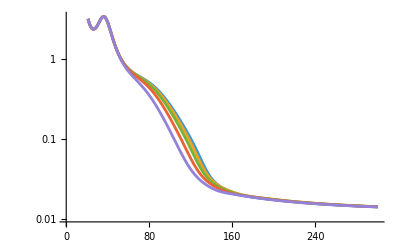

```mathematica
ListLinePlot[{Transpose[{T,c2data[[1]]}],Transpose[{T,c2data[[2]]}],Transpose[{T,c2data[[3]]}],Transpose[{T,c2data[[4]]}],Transpose[{T,c2data[[5]]}]},ScalingFunctions->"Log"]
```

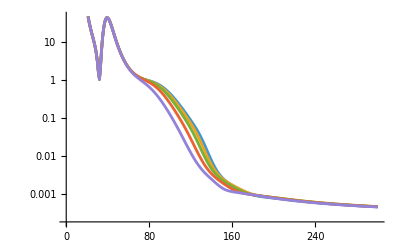

```mathematica
ListLinePlot[{Transpose[{T,-c3data[[1]]}],Transpose[{T,-c3data[[2]]}],Transpose[{T,-c3data[[3]]}],Transpose[{T,-c3data[[4]]}],Transpose[{T,-c3data[[5]]}]},ScalingFunctions->"Log"]
```

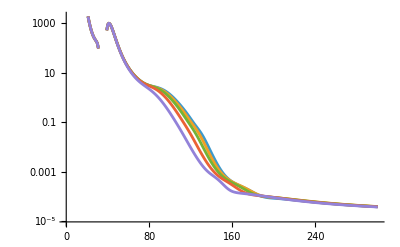

```mathematica
ListLinePlot[{Transpose[{T,c4data[[1]]}],Transpose[{T,c4data[[2]]}],Transpose[{T,c4data[[3]]}],Transpose[{T,c4data[[4]]}],Transpose[{T,c4data[[5]]}]},ScalingFunctions->"Log"]
```

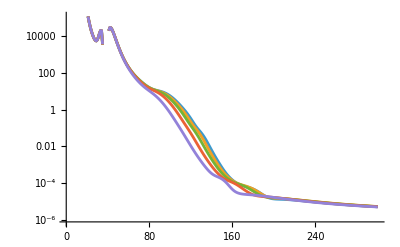

```mathematica
ListLinePlot[{Transpose[{T,-c5data[[1]]}],Transpose[{T,-c5data[[2]]}],Transpose[{T,-c5data[[3]]}],Transpose[{T,-c5data[[4]]}],Transpose[{T,-c5data[[5]]}]},ScalingFunctions->"Log"]
```

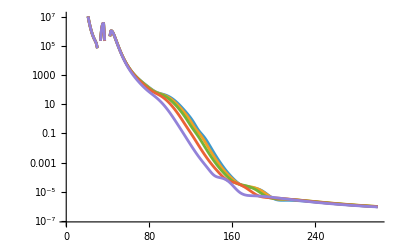

```mathematica
ListLinePlot[{Transpose[{T,c6data[[1]]}],Transpose[{T,c6data[[2]]}],Transpose[{T,c6data[[3]]}],Transpose[{T,c6data[[4]]}],Transpose[{T,c6data[[5]]}]},ScalingFunctions->"Log"]
```